( | E_0 | E_in | E_x1 | E_y1 | E_x2 | E_y2 | E_as | E_LO | E_a | E_b
E_0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_in | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_x1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_y1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_x2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_y2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
E_as | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
E_LO | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
E_a | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
E_b | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0)

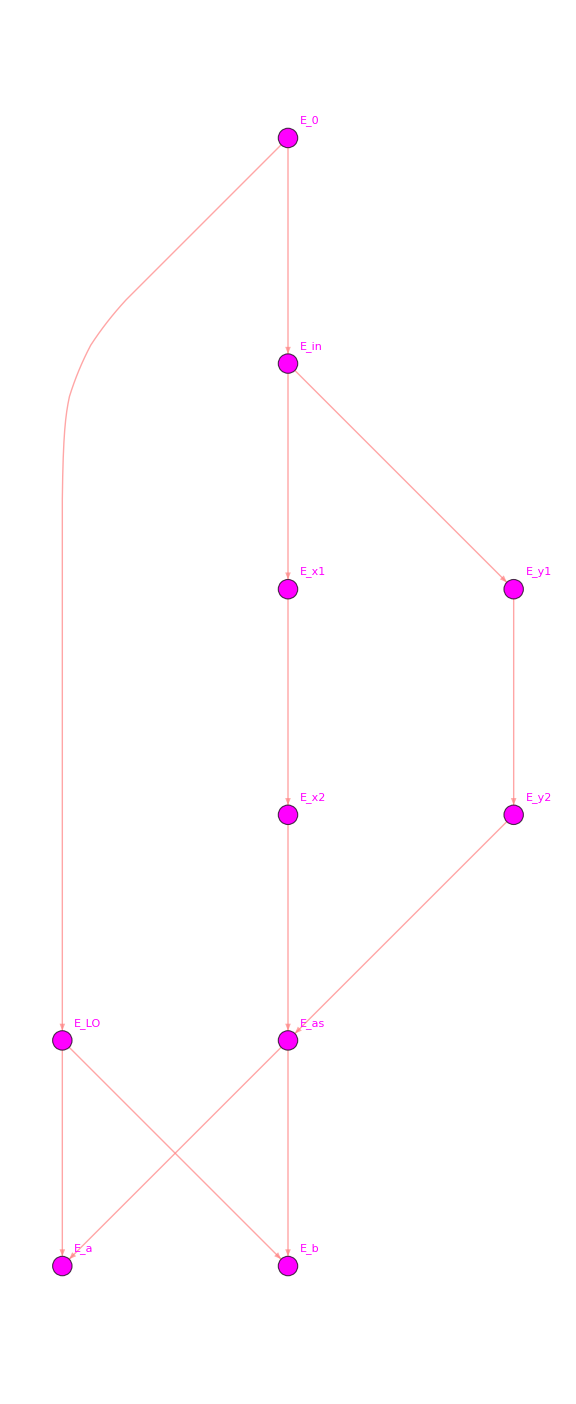

```mathematica
nodes={"E_0","E_in","E_x1","E_y1","E_x2","E_y2","E_as","E_LO","E_a","E_b"};

A={(*E_0 E_in E_x1 E_y1 E_x2 E_y2 E_as E_LO E_a E_b*)
(*E_0*){0,0,0,0,0,0,0,0,0,0},
(*E_in*){1,0,0,0,0,0,0,0,0,0},
(*E_x1*){0,1,0,0,0,0,0,0,0,0},
(*E_y1*){0,1,0,0,0,0,0,0,0,0},
(*E_x2*){0,0,1,0,0,0,0,0,0,0},
(*E_y2*){0,0,0,1,0,0,0,0,0,0},
(*E_as*){0,0,0,0,1,1,0,0,0,0},
(*E_LO*){1,0,0,0,0,0,0,0,0,0},
(*E_a*){0,0,0,0,0,0,1,1,0,0},
(*E_b*){0,0,0,0,0,0,1,1,0,0}};


MatrixForm[A,TableHeadings->{nodes,nodes}]

(*directed graph to help me visualize*)
edges=Flatten[Table[If[A[[i,j]]==1,DirectedEdge[nodes[[j]],nodes[[i]]],Nothing],{j,Length[nodes]},{i,Length[nodes]}]];

Graph[edges,VertexLabels->"Name",ImageSize->Large,EdgeStyle->Pink,VertexStyle->Magenta]
```

```mathematica
nodes={"E0","Ein","EX","EY","EXret","EYret","EAS","ELO","EA","EB"};

M={(*E_0 E_in E_x1 E_y1 E_x2 E_y2 E_as E_LO E_a E_b*)
(*E_0*){0,0,0,0,0,0,0,0,0,0},
(*E_in*){t_LO,0,0,0,0,0,0,0,0,0},
(*E_x1*){0,t_BS*Exp[-I*k*Lx],0,0,0,0,0,0,0,0},
(*E_y1*){0,-r_BS*Exp[-I*k*Ly],0,0,0,0,0,0,0,0},
(*E_x2*){0,0,-r_x*Exp[-I*k*Lx],0,0,0,0,0,0,0},
(*E_y2*){0,0,0,-r_y*Exp[-I*k*Ly],0,0,0,0,0,0},
(*E_as*){0,0,0,0,r_BS,t_BS,0,0,0,0},
(*E_LO*){-r_LO*Exp[-I*ϕ_HD],0,0,0,0,0,0,0,0,0},
(*E_a*){0,0,0,0,0,0,t_HD,r_HD,0,0},
(*E_b*){0,0,0,0,0,0,-r_HD,t_HD,0,0}}

MatrixForm[M,TableHeadings->{nodes,nodes}]
```

{{0,0,0,0,0,0,0,0,0,0},{t_LO,0,0,0,0,0,0,0,0,0},{0,ⅇ^(-ⅈ k Lx) t_BS,0,0,0,0,0,0,0,0},{0,-ⅇ^(-ⅈ k Ly) r_BS,0,0,0,0,0,0,0,0},{0,0,-ⅇ^(-ⅈ k Lx) r_x,0,0,0,0,0,0,0},{0,0,0,-ⅇ^(-ⅈ k Ly) r_y,0,0,0,0,0,0},{0,0,0,0,r_BS,t_BS,0,0,0,0},{-ⅇ^(-ⅈ ϕ_HD) r_LO,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,t_HD,r_HD,0,0},{0,0,0,0,0,0,-r_HD,t_HD,0,0}}

( | E0 | Ein | EX | EY | EXret | EYret | EAS | ELO | EA | EB
E0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ein | t_LO | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
EX | 0 | ⅇ^(-ⅈ k Lx) t_BS | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
EY | 0 | -ⅇ^(-ⅈ k Ly) r_BS | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
EXret | 0 | 0 | -ⅇ^(-ⅈ k Lx) r_x | 0 | 0 | 0 | 0 | 0 | 0 | 0
EYret | 0 | 0 | 0 | -ⅇ^(-ⅈ k Ly) r_y | 0 | 0 | 0 | 0 | 0 | 0
EAS | 0 | 0 | 0 | 0 | r_BS | t_BS | 0 | 0 | 0 | 0
ELO | -ⅇ^(-ⅈ ϕ_HD) r_LO | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
EA | 0 | 0 | 0 | 0 | 0 | 0 | t_HD | r_HD | 0 | 0
EB | 0 | 0 | 0 | 0 | 0 | 0 | -r_HD | t_HD | 0 | 0)

## Question #1

### 1.1 - Adjacency Matrix

```mathematica
nodes={"Ein","EX1","EY1","EX2","EY2","EAS","ELO","EA","EB"};

M={(*Ein EX1 EY1 EX2 EY2 EAS ELO EA EB*)
(*Ein*){0,0,0,0,0,0,0,0,0},
(*EX1*){tBS*Exp[-I*k*Lx],0,0,0,0,0,0,0,0},
(*EY1*){-rBS*Exp[-I*k*Ly],0,0,0,0,0,0,0,0},
(*EX2*){0,-rx*Exp[-I*k*Lx],0,0,0,0,0,0,0},
(*EY2*){0,0,-ry*Exp[-I*k*Ly],0,0,0,0,0,0},
(*EAS*){0,0,0,rBS,tBS,0,0,0,0},
(*ELO*){-rLO*Exp[-I*ϕHD],0,0,0,0,0,0,0,0},
(*EA*){0,0,0,0,0,tHD,rHD,0,0},
(*EB*){0,0,0,0,0,-rHD,tHD,0,0}};

MatrixForm[M,TableHeadings->{nodes,nodes}]
```

( | Ein | EX1 | EY1 | EX2 | EY2 | EAS | ELO | EA | EB
Ein | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
EX1 | ⅇ^(-ⅈ k Lx) tBS | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
EY1 | -ⅇ^(-ⅈ k Ly) rBS | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
EX2 | 0 | -ⅇ^(-ⅈ k Lx) rx | 0 | 0 | 0 | 0 | 0 | 0 | 0
EY2 | 0 | 0 | -ⅇ^(-ⅈ k Ly) ry | 0 | 0 | 0 | 0 | 0 | 0
EAS | 0 | 0 | 0 | rBS | tBS | 0 | 0 | 0 | 0
ELO | -ⅇ^(-ⅈ ϕHD) rLO | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
EA | 0 | 0 | 0 | 0 | 0 | tHD | rHD | 0 | 0
EB | 0 | 0 | 0 | 0 | 0 | -rHD | tHD | 0 | 0)

### 1.2 - Electric Field Transfer Functions

```mathematica
id=IdentityMatrix[Length[nodes]];
IminusM=id-M;
T=Inverse[IminusM];


MatrixForm[T,TableHeadings->{nodes,nodes}]

T[[Position[nodes,"EA"][[1,1]],Position[nodes,"Ein"][[1,1]]]]

TF[from_String,to_String]:=T[[Position[nodes,to][[1,1]],Position[nodes,from][[1,1]]]]

Print["E_PDA/E_in = ",TF["Ein","EA"]]
Print["E_PDB/E_in = ",TF["Ein","EB"]]
Print["E_as/E_in = ",TF["Ein","EAS"]]
```

( | Ein | EX1 | EY1 | EX2 | EY2 | EAS | ELO | EA | EB
Ein | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
EX1 | ⅇ^(-ⅈ k Lx) tBS | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
EY1 | -ⅇ^(-ⅈ k Ly) rBS | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
EX2 | -ⅇ^(-2 ⅈ k Lx) rx tBS | -ⅇ^(-ⅈ k Lx) rx | 0 | 1 | 0 | 0 | 0 | 0 | 0
EY2 | ⅇ^(-2 ⅈ k Ly) rBS ry | 0 | -ⅇ^(-ⅈ k Ly) ry | 0 | 1 | 0 | 0 | 0 | 0
EAS | -ⅇ^(-2 ⅈ k Lx) rBS rx tBS+ⅇ^(-2 ⅈ k Ly) rBS ry tBS | -ⅇ^(-ⅈ k Lx) rBS rx | -ⅇ^(-ⅈ k Ly) ry tBS | rBS | tBS | 1 | 0 | 0 | 0
ELO | -ⅇ^(-ⅈ ϕHD) rLO | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
EA | -ⅇ^(-ⅈ ϕHD) rHD rLO-ⅇ^(-2 ⅈ k Lx) rBS rx tBS tHD+ⅇ^(-2 ⅈ k Ly) rBS ry tBS tHD | -ⅇ^(-ⅈ k Lx) rBS rx tHD | -ⅇ^(-ⅈ k Ly) ry tBS tHD | rBS tHD | tBS tHD | tHD | rHD | 1 | 0
EB | ⅇ^(-2 ⅈ k Lx) rBS rHD rx tBS-ⅇ^(-2 ⅈ k Ly) rBS rHD ry tBS-ⅇ^(-ⅈ ϕHD) rLO tHD | ⅇ^(-ⅈ k Lx) rBS rHD rx | ⅇ^(-ⅈ k Ly) rHD ry tBS | -rBS rHD | -rHD tBS | -rHD | tHD | 0 | 1)

-ⅇ^(-ⅈ ϕHD) rHD rLO-ⅇ^(-2 ⅈ k Lx) rBS rx tBS tHD+ⅇ^(-2 ⅈ k Ly) rBS ry tBS tHD

E_PDA/E_in = -ⅇ^(-ⅈ ϕHD) rHD rLO-ⅇ^(-2 ⅈ k Lx) rBS rx tBS tHD+ⅇ^(-2 ⅈ k Ly) rBS ry tBS tHD

E_PDB/E_in = ⅇ^(-2 ⅈ k Lx) rBS rHD rx tBS-ⅇ^(-2 ⅈ k Ly) rBS rHD ry tBS-ⅇ^(-ⅈ ϕHD) rLO tHD

E_as/E_in = -ⅇ^(-2 ⅈ k Lx) rBS rx tBS+ⅇ^(-2 ⅈ k Ly) rBS ry tBS

### 1.3 - Substitutions & 1.4 - Power Transfer Functions

```mathematica
(*replacing all the t_BS and r_BS with 1/sqrt2, 
also assuming end test masses have perfect reflectivities rx=ry=1, and assuming homodyne BS is a perfect 50/50 for simplicity*)
M50=M/. {tBS->1/Sqrt[2],rBS->1/Sqrt[2],rx->1,ry->1, tHD->1/Sqrt[2], rHD->1/Sqrt[2]};

(*recalculating TFs with these t_BS and r_BS subs*)
T50=Inverse[IdentityMatrix[Length[nodes]]-M50];

TEPDA=TF50["Ein","EA"];
TEPDB=TF50["Ein","EB"];

(*helper function with substituted matrix*)
TF50[from_String,to_String]:=T50[[Position[nodes,to][[1,1]],Position[nodes,from][[1,1]]]]

(*replacing kLx with phix and kLy with phiy*)
TEPDAϕ=TEPDA/. {k*Lx->ϕx,k*Ly->ϕy};
TEPDBϕ=TEPDB/. {k*Lx->ϕx,k*Ly->ϕy};

(*replacing phix and phiy with appropriate phiD and phiC expressions, using the ones given in the HW assignment*)
phaseSub={ϕx->ϕc+ϕd,ϕy->ϕc-ϕd};
TEPDAdc=FullSimplify[TEPDAϕ/. phaseSub];
TEPDBdc=FullSimplify[TEPDBϕ/. phaseSub];

Row[{"E_PDA/E_in = ",TEPDAdc}]
Row[{"E_PDB/E_in = ",TEPDBdc}]

PPDA=FullSimplify[ComplexExpand[TEPDAdc*Conjugate[TEPDAdc]]]
PPDB=FullSimplify[ComplexExpand[TEPDBdc*Conjugate[TEPDBdc]]]

(*Using P = |E|^2, finding power transfer functions*)
Print["P_PDA/P_in = ",PPDA]
Print["P_PDB/P_in = ",PPDB]
```

```mathematica
"E_PDA/E_in = "(-ⅇ^(-ⅈ ϕHD) rLO+2 ⅈ ⅇ^(-2 ⅈ ϕc) Cos[ϕd] Sin[ϕd])/(√2)
```

E_PDB/E_in = (-ⅇ^(-2 ⅈ (ϕc-ϕd))+ⅇ^(-2 ⅈ (ϕc+ϕd))-2 ⅇ^(-ⅈ ϕHD) rLO)/(2 √2)

1/4 (1+2 rLO^2-Cos[4 ϕd]-4 rLO Sin[2 ϕd] Sin[2 ϕc-ϕHD])

1/4 (1+2 rLO^2-Cos[4 ϕd]+4 rLO Sin[2 ϕd] Sin[2 ϕc-ϕHD])

P_PDA/P_in = 1/4 (1+2 rLO^2-Cos[4 ϕd]-4 rLO Sin[2 ϕd] Sin[2 ϕc-ϕHD])

P_PDB/P_in = 1/4 (1+2 rLO^2-Cos[4 ϕd]+4 rLO Sin[2 ϕd] Sin[2 ϕc-ϕHD])

### 1.5 - Interpretation

- How do the power TF’s depend on homodyne angle and com/diff Michelson phases?
- Can we manipulate homodyne angle to detect differential phase?
- Can you think of any more problems we might run into if you actually tried to set up a homodyned Michelson?

Used Claude for following plots to hep me wrap my brain around these results

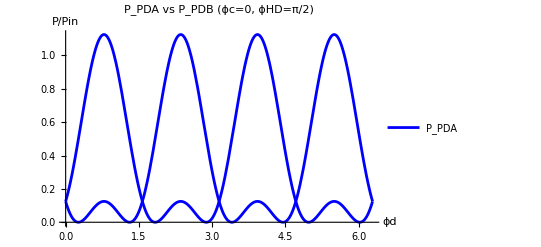

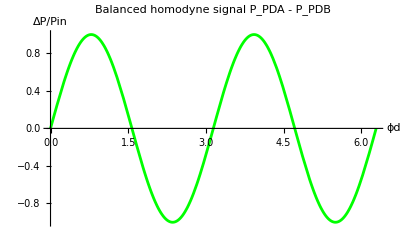

```mathematica
rLO=0.5;

Plot[{1/4*(1+2*rLO^2-Cos[4*ϕd]-4*rLO*Sin[2*ϕd]*Sin[2*0-ϕHD]),1/4*(1+2*rLO^2-Cos[4*ϕd]+4*rLO*Sin[2*ϕd]*Sin[2*0-ϕHD])}/. ϕHD->Pi/2,{ϕd,0,2*Pi},PlotLegends->{"P_PDA","P_PDB"},AxesLabel->{"ϕd","P/Pin"},PlotLabel->"P_PDA vs P_PDB (ϕc=0, ϕHD=π/2)",PlotStyle->{Red,Blue}]
(*Most importantly:plot the difference-balanced homodyne signal*)
Plot[(1/4*(1+2*rLO^2-Cos[4*ϕd]-4*rLO*Sin[2*ϕd]*Sin[2*ϕc-ϕHD])-1/4*(1+2*rLO^2-Cos[4*ϕd]+4*rLO*Sin[2*ϕd]*Sin[2*ϕc-ϕHD]))/. {ϕc->0,ϕHD->Pi/2},{ϕd,0,2*Pi},AxesLabel->{"ϕd","ΔP/Pin"},PlotLabel->"Balanced homodyne signal P_PDA - P_PDB",PlotStyle->Green]
```

-Graphics3D-

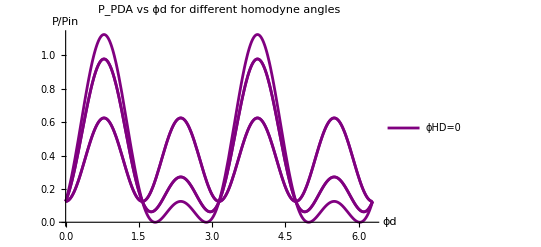

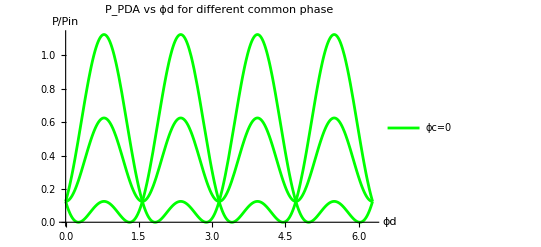

```mathematica
rLO=0.5; 

(*3D plot:vary both phid and phiHD,fix phic*)
Plot3D[1/4*(1+2*rLO^2-Cos[4*ϕd]-4*rLO*Sin[2*ϕd]*Sin[2*ϕc-ϕHD])/. {ϕc->0},{ϕd,0,2*Pi},{ϕHD,0,2*Pi},AxesLabel->{"ϕd","ϕHD","P/Pin"},PlotLabel->"P_PDA vs differential phase and homodyne angle",ColorFunction->"SunsetColors",PlotRange->All]

(*Or 2D:vary phid for different homodyne angles*)
Plot[Table[1/4*(1+2*rLO^2-Cos[4*ϕd]-4*rLO*Sin[2*ϕd]*Sin[2*ϕc-ϕHD])/. {ϕc->0},{ϕHD,{0,Pi/4,Pi/2,3*Pi/4,Pi}}],{ϕd,0,2*Pi},PlotLegends->{"ϕHD=0","ϕHD=π/4","ϕHD=π/2","ϕHD=3π/4","ϕHD=π"},AxesLabel->{"ϕd","P/Pin"},PlotLabel->"P_PDA vs ϕd for different homodyne angles",PlotStyle->{Red,Orange,Green,Blue,Purple}]

(*2D:vary phic to see common mode effect*)
Plot[Table[1/4*(1+2*rLO^2-Cos[4*ϕd]-4*rLO*Sin[2*ϕd]*Sin[2*ϕc-ϕHD])/. {ϕHD->Pi/2},{ϕc,{0,Pi/4,Pi/2}}],{ϕd,0,2*Pi},PlotLegends->{"ϕc=0","ϕc=π/4","ϕc=π/2"},AxesLabel->{"ϕd","P/Pin"},PlotLabel->"P_PDA vs ϕd for different common phase",PlotStyle->{Red,Blue,Green}]
```

## Question #2

```mathematica
nodes={"E_in","E_x","E_y","E_refl","E_as"};

A={(*E_in E_x1 E_y1 E_x2 E_y2 E_refl E_as*)
(*E_in*){0,0,0,0,0},
(*E_x*){1,0,0,0,0},
(*E_y*){1,0,0,0,0},
(*E_refl*){0,1,1,0,0},
(*E_as*){0,1,1,0,0}};

MatrixForm[A,TableHeadings->{nodes,nodes}]

(*directed graph*)
edges=Flatten[Table[If[A[[i,j]]==1,DirectedEdge[nodes[[j]],nodes[[i]]],Nothing],{j,Length[nodes]},{i,Length[nodes]}]];

Graph[edges,VertexLabels->"Name",ImageSize->Large,EdgeStyle->Pink,VertexStyle->Magenta]
```

( | E_in | E_x | E_y | E_refl | E_as
E_in | 0 | 0 | 0 | 0 | 0
E_x | 1 | 0 | 0 | 0 | 0
E_y | 1 | 0 | 0 | 0 | 0
E_refl | 0 | 1 | 1 | 0 | 0
E_as | 0 | 1 | 1 | 0 | 0)

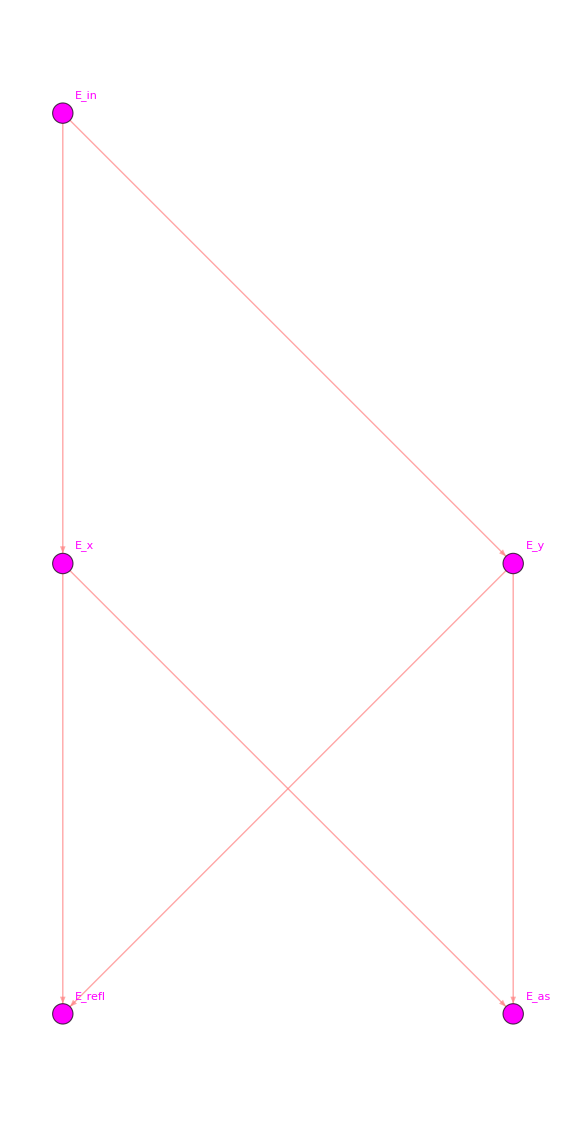

### 2.1 - Field Transfer Functions

```mathematica
nodes={"E_in","E_x","E_y","E_refl","E_as"};

M={(*E_in E_x1 E_y1 E_x2 E_y2 E_refl E_as*)
(*E_in*){0,0,0,0,0},
(*E_x*){t_BS*Exp[-2*I*ϕx]*-r_x,0,0,0,0},
(*E_y*){-r_BS*Exp[-2*I*ϕy]*-r_y,0,0,0,0},
(*E_refl*){0,t_BS,-r_BS,0,0},
(*E_as*){0,r_BS,t_BS,0,0}};

MatrixForm[M,TableHeadings->{nodes,nodes}]
```

( | E_in | E_x | E_y | E_refl | E_as
E_in | 0 | 0 | 0 | 0 | 0
E_x | -ⅇ^(-2 ⅈ ϕx) r_x t_BS | 0 | 0 | 0 | 0
E_y | ⅇ^(-2 ⅈ ϕy) r_BS r_y | 0 | 0 | 0 | 0
E_refl | 0 | t_BS | -r_BS | 0 | 0
E_as | 0 | r_BS | t_BS | 0 | 0)

```mathematica
id=IdentityMatrix[Length[nodes]];
IminusB=id-M;
T=Inverse[IminusM];

MatrixForm[T,TableHeadings->{nodes,nodes}]

TF[from_String,to_String]:=T[[Position[nodes,to][[1,1]],Position[nodes,from][[1,1]]]]

Print["E_x/E_in = ",TF["E_in","E_x"]]
Print["E_y/E_in = ",TF["E_in","E_y"]]
Print["E_as/E_in = ",TF["E_in","E_as"]]
```

( | E_in | E_x | E_y | E_refl | E_as
E_in | 1 | 0 | 0 | 0 | 0
E_x | -ⅇ^(-2 ⅈ ϕx) r_x t_BS | 1 | 0 | 0 | 0
E_y | ⅇ^(-2 ⅈ ϕy) r_BS r_y | 0 | 1 | 0 | 0
E_refl | -ⅇ^(-2 ⅈ ϕy) r_BS^2 r_y-ⅇ^(-2 ⅈ ϕx) r_x t_BS^2 | t_BS | -r_BS | 1 | 0
E_as | -ⅇ^(-2 ⅈ ϕx) r_BS r_x t_BS+ⅇ^(-2 ⅈ ϕy) r_BS r_y t_BS | r_BS | t_BS | 0 | 1)

E_x/E_in = -ⅇ^(-2 ⅈ ϕx) r_x t_BS

E_y/E_in = ⅇ^(-2 ⅈ ϕy) r_BS r_y

E_as/E_in = -ⅇ^(-2 ⅈ ϕx) r_BS r_x t_BS+ⅇ^(-2 ⅈ ϕy) r_BS r_y t_BS

```mathematica
(*adding in expression for E_in*)
Einput=E0*Exp[I*ω0*t];

(*new transfer functions with correct E_in*)
T=Inverse[IdentityMatrix[Length[nodes]]-M];

TEas=TF["E_in","E_as"]*Einput;
TEx=TF["E_in","E_x"]*Einput;
TEy=TF["E_in","E_y"]*Einput;

Print["E_as = ",TEas]
Print["E_x = ",TEx]
Print["E_y = ",TEy]
```

E_as = ⅇ^(ⅈ t ω0) E0 (-ⅇ^(-2 ⅈ ϕx) r_BS r_x t_BS+ⅇ^(-2 ⅈ ϕy) r_BS r_y t_BS)

E_x = -ⅇ^(-2 ⅈ ϕx+ⅈ t ω0) E0 r_x t_BS

E_y = ⅇ^(-2 ⅈ ϕy+ⅈ t ω0) E0 r_BS r_y

### 2.2 - End Mirror Modulation

```mathematica
(*adding time-dependent common modulation ΓCos[ω*t] to phase accumulated from round trip down arms*)
TExmod=TEx/. {ϕx -> ϕx0 + ΓCos[ω*t],ϕy-> ϕy0+ ΓCos[ω*t]};
TEymod=TEy/. {ϕx -> ϕx0 + ΓCos[ω*t],ϕy-> ϕy0+ ΓCos[ω*t]};

Row[{"E_x/E_in = ",TExmod}]
Row[{"E_y/E_in = ",TEymod}]
```

E_x/E_in = -ⅇ^(ⅈ t ω0-2 ⅈ ((Lx ω0)/c+ΓCos[t ω])) E0 r_x t_BS

E_y/E_in = ⅇ^(ⅈ t ω0-2 ⅈ ((Ly ω0)/c+ΓCos[t ω])) E0 r_BS r_y

```mathematica
(*in the above expressions, the three distinct fields are encoded in the phase modulated exponent according to Jacobi-Anger as follows*)

(*assumng perfect BS for simplicity)*)
rBS=1/Sqrt[2];
tBS=1/Sqrt[2];

(*0th and 1st Bessel functions, 2Gamma for round trip in the arms*)
J0=BesselJ[0,2*Γ];
J1=BesselJ[1,2*Γ];

(*explicitly defining phases for each freq and each arm*)
ϕx0=ω0/c*Lx;
ϕxup=(ω0+ω)/c*Lx;
ϕxlow=(ω0-ω)/c*Lx;

ϕy0=ω0/c*Ly;
ϕyup=(ω0+ω)/c*Ly;
ϕylow=(ω0-ω)/c*Ly;

(*expanded E_x and E_y to show three distinct fields*)
Ex=-tBS*rx*E0*(J0*Exp[I*ω0*t]*Exp[-2I*ϕx0]+(-I*J1)*Exp[I*(ω0+ω)*t]*Exp[-2I*ϕxup]+(-I*J1)*Exp[I*(ω0-ω)*t]*Exp[-2I*ϕxlow]);
Ey=rBS*ry*E0*(J0*Exp[I*ω0*t]*Exp[-2I*ϕy0]+(-I*J1)*Exp[I*(ω0+ω)*t]*Exp[-2I*ϕyup]+(-I*J1)*Exp[I*(ω0-ω)*t]*Exp[-2I*ϕylow]);

Row[{"Ex = ",Ex}]
Row[{"Ey = ",Ey}]
Row[{"Eas = ",Eas}]
```

Ex = -(E0 rx (ⅇ^(-(2 ⅈ Lx ω0)/c+ⅈ t ω0) BesselJ[0,2 Γ]-ⅈ ⅇ^(-(2 ⅈ Lx (-ω+ω0))/c+ⅈ t (-ω+ω0)) BesselJ[1,2 Γ]-ⅈ ⅇ^(-(2 ⅈ Lx (ω+ω0))/c+ⅈ t (ω+ω0)) BesselJ[1,2 Γ]))/(√2)

Ey = (E0 ry (ⅇ^(-(2 ⅈ Ly ω0)/c+ⅈ t ω0) BesselJ[0,2 Γ]-ⅈ ⅇ^(-(2 ⅈ Ly (-ω+ω0))/c+ⅈ t (-ω+ω0)) BesselJ[1,2 Γ]-ⅈ ⅇ^(-(2 ⅈ Ly (ω+ω0))/c+ⅈ t (ω+ω0)) BesselJ[1,2 Γ]))/(√2)

Eas = -1/2 E0 rx (ⅇ^(-(2 ⅈ Lx ω0)/c+ⅈ t ω0) BesselJ[0,2 Γ]-ⅈ ⅇ^(-(2 ⅈ Lx (-ω+ω0))/c+ⅈ t (-ω+ω0)) BesselJ[1,2 Γ]-ⅈ ⅇ^(-(2 ⅈ Lx (ω+ω0))/c+ⅈ t (ω+ω0)) BesselJ[1,2 Γ])+1/2 E0 ry (ⅇ^(-(2 ⅈ Ly ω0)/c+ⅈ t ω0) BesselJ[0,2 Γ]-ⅈ ⅇ^(-(2 ⅈ Ly (-ω+ω0))/c+ⅈ t (-ω+ω0)) BesselJ[1,2 Γ]-ⅈ ⅇ^(-(2 ⅈ Ly (ω+ω0))/c+ⅈ t (ω+ω0)) BesselJ[1,2 Γ])

### 2.3 - Propagate to the antisymmetric port

```mathematica
Eas=rBS*Ex+tBS*Ey;

Print["E_as = ",Eas]
Row[{"E_as/E_in = ",TFEas= Eas/E0}]
```

E_as = -1/2 E0 rx (ⅇ^(-(2 ⅈ Lx ω0)/c+ⅈ t ω0) BesselJ[0,2 Γ]-ⅈ ⅇ^(-(2 ⅈ Lx (-ω+ω0))/c+ⅈ t (-ω+ω0)) BesselJ[1,2 Γ]-ⅈ ⅇ^(-(2 ⅈ Lx (ω+ω0))/c+ⅈ t (ω+ω0)) BesselJ[1,2 Γ])+1/2 E0 ry (ⅇ^(-(2 ⅈ Ly ω0)/c+ⅈ t ω0) BesselJ[0,2 Γ]-ⅈ ⅇ^(-(2 ⅈ Ly (-ω+ω0))/c+ⅈ t (-ω+ω0)) BesselJ[1,2 Γ]-ⅈ ⅇ^(-(2 ⅈ Ly (ω+ω0))/c+ⅈ t (ω+ω0)) BesselJ[1,2 Γ])

E_as/E_in = (-1/2 E0 rx (ⅇ^(-(2 ⅈ Lx ω0)/c+ⅈ t ω0) BesselJ[0,2 Γ]-ⅈ ⅇ^(-(2 ⅈ Lx (-ω+ω0))/c+ⅈ t (-ω+ω0)) BesselJ[1,2 Γ]-ⅈ ⅇ^(-(2 ⅈ Lx (ω+ω0))/c+ⅈ t (ω+ω0)) BesselJ[1,2 Γ])+1/2 E0 ry (ⅇ^(-(2 ⅈ Ly ω0)/c+ⅈ t ω0) BesselJ[0,2 Γ]-ⅈ ⅇ^(-(2 ⅈ Ly (-ω+ω0))/c+ⅈ t (-ω+ω0)) BesselJ[1,2 Γ]-ⅈ ⅇ^(-(2 ⅈ Ly (ω+ω0))/c+ⅈ t (ω+ω0)) BesselJ[1,2 Γ]))/E0

### 2.4 - Calculate the power response

```mathematica
TFEas=(-(1/2)*rx*(Exp[-((2I*Lx*ω0)/c)+I*t*ω0]*J0-I*Exp[-((2I*Lx*(-ω+ω0))/c)+I*t*(-ω+ω0)]*J1-I*Exp[-((2I*Lx*(ω+ω0))/c)+I*t*(ω+ω0)]*J1)+1/2*ry*(Exp[-((2I*Ly*ω0)/c)+I*t*ω0]*J0-I*Exp[-((2I*Ly*(-ω+ω0))/c)+I*t*(-ω+ω0)]*J1-I*Exp[-((2I*Ly*(ω+ω0))/c)+I*t*(ω+ω0)]*J1));

phaseSub1={Lx*ω0/c->ϕx0,Ly*ω0/c->ϕy0,Lx*(ω0+ω)/c->ϕxup,Ly*(ω0+ω)/c->ϕyup,Lx*(ω0-ω)/c->ϕxlow,Ly*(ω0-ω)/c->ϕylow, rx -> r, ry -> r};

TFEasPhi=TFEas/. phaseSub1;

phaseSub2={ϕx0->ϕc0+ϕd0,ϕy0->ϕc0-ϕd0,ϕxup->ϕcup+ϕdup,ϕyup->ϕcup-ϕdup,ϕxlow->ϕclow+ϕdlow,ϕylow->ϕclow-ϕdlow};

TFEasdc=FullSimplify[TFEasPhi/. phaseSub2];
Row[{"E_as/E_in = ",TFEasdc}]
```

E_as/E_in = 1/2 ⅇ^(-ⅈ t (ω-ω0)) r (ⅇ^(-2 ⅈ (ϕc0+ϕd0)+ⅈ t ω) (-1+ⅇ^(4 ⅈ ϕd0)) BesselJ[0,2 Γ]-ⅈ ⅇ^(-2 ⅈ (ϕclow+ϕcup+ϕdlow+ϕdup)) (-ⅇ^(2 ⅈ (ϕcup+ϕdup))+ⅇ^(2 ⅈ (ϕcup+2 ϕdlow+ϕdup))-ⅇ^(2 ⅈ (ϕclow+ϕdlow+t ω))+ⅇ^(2 ⅈ (ϕclow+ϕdlow+2 ϕdup+t ω))) BesselJ[1,2 Γ])

```mathematica
phaseSub3={ϕc0->ϕc,ϕd0->ϕd,ϕcup->ϕc,ϕdup->ϕd,ϕclow->ϕc,ϕdlow->ϕd};

TFEasdcSimple=FullSimplify[TFEasdc/. phaseSub3];

Row[{"E_as/E_in= ",TFEasdcSimple}]
```

E_as/E_in= 1/2 ⅇ^(-2 ⅈ (ϕc+ϕd)+ⅈ t ω0) (-1+ⅇ^(4 ⅈ ϕd)) r (BesselJ[0,2 Γ]-2 ⅈ BesselJ[1,2 Γ] Cos[t ω])

```mathematica
$Assumptions={ϕc∈Reals,ϕd∈Reals,r∈Reals,Γ∈Reals,t∈Reals,ω∈Reals,ω0∈Reals};

PEas=FullSimplify[TFEasdcSimple*Conjugate[TFEasdcSimple]];
Print["P_as/P_in = ",PEas]
```

P_as/P_in = r^2 (BesselJ[0,2 Γ]^2+4 BesselJ[1,2 Γ]^2 Cos[t ω]^2) Sin[2 ϕd]^2